```mathematica
SetDirectory["/home/meike/Documents/"];
Get["PlotTheme.m"]
$PlotTheme="Publication";
Needs["ErrorBarPlots`"];
SetDirectory[]; 
path="/home/meike/Documents/literature/conferences/Elisbon/day07/exercises/";
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
gridt={};
For[t = 0, t ≤ 19000, t+=1000, 
grid=Import[path<>"grid_t"<>ToString[t]<>".dat"];
AppendTo[gridt,grid];
]
```

```mathematica
Max[gridt[[1]]]
```

0.999211

```mathematica
Manipulate[ListDensityPlot[gridt[[step]],ColorFunction->ColorData[{"RedBlueTones",{0,1}}],ColorFunctionScaling->False,PlotLegends->Automatic],{step,1,Length[gridt],1}]
```

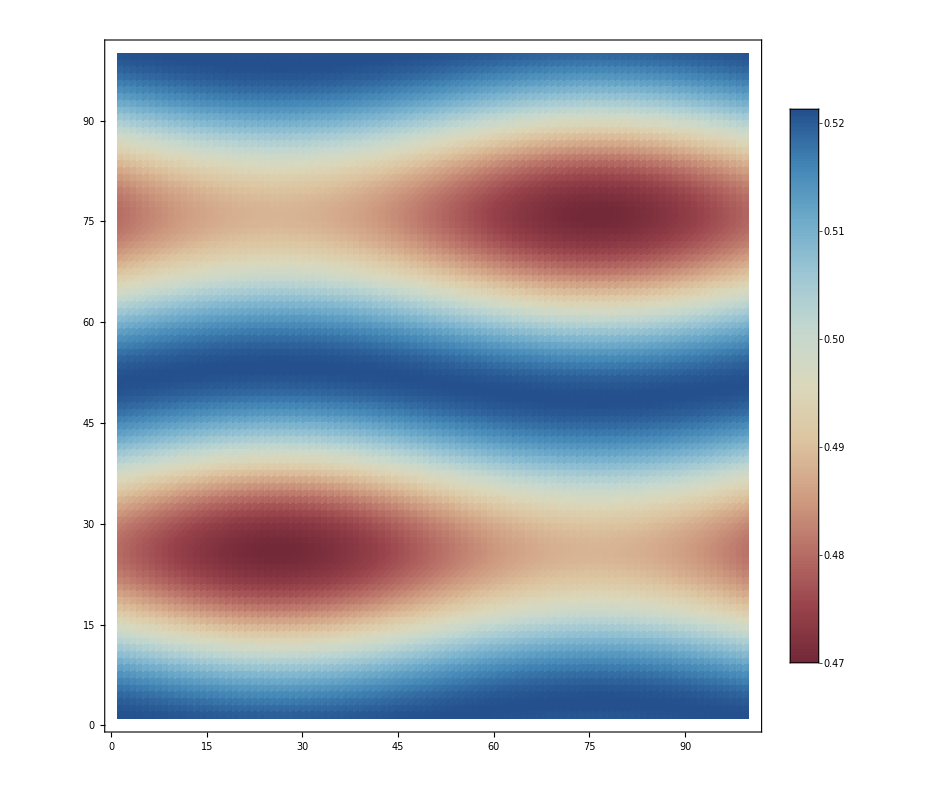

```mathematica
ListDensityPlot[gridt[[3]],ColorFunction->ColorData[{"RedBlueTones",{0,1}}],PlotLegends->Automatic,ImageSize->800]
```

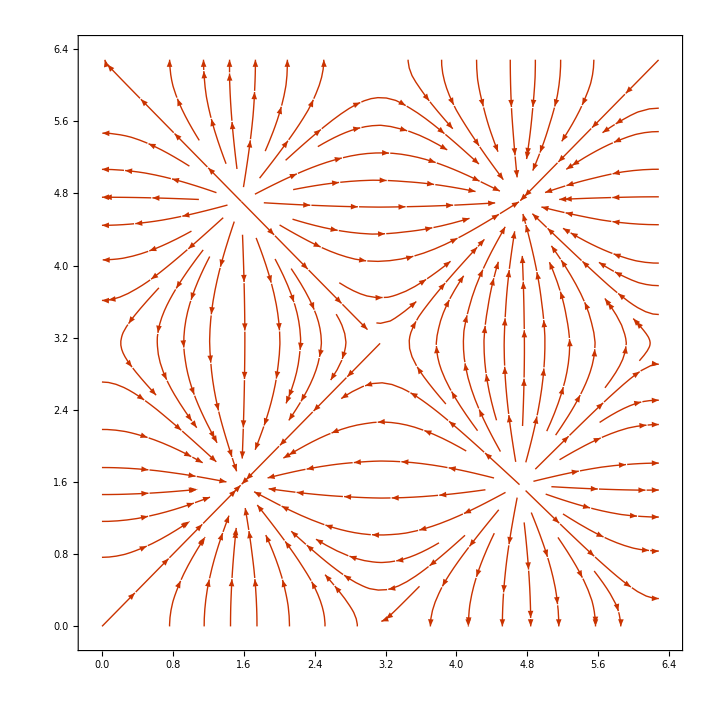

```mathematica
StreamPlot[{0.5*Cos[x]*Sin[y],0.5*Sin[x]*Cos[y]},{x,0,2π},{y,0,2π}]
```

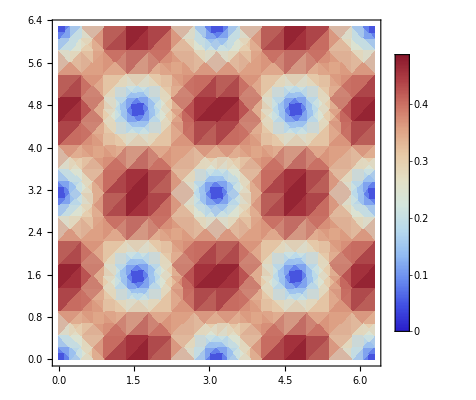

```mathematica
DensityPlot[Norm[{0.5*Cos[x]*Sin[y],0.5*Sin[x]*Cos[y]}],{x,0,2π},{y,0,2π},PlotLegends->Automatic]
```

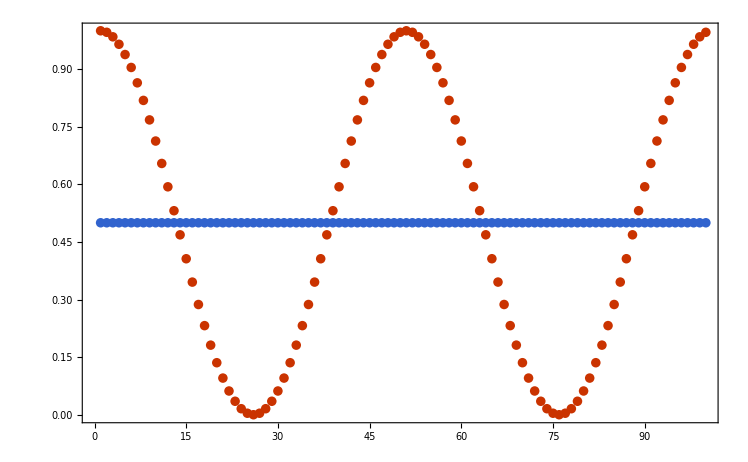

```mathematica
ListPlot[{gridt[[1,All,10]],gridt[[-1,All,10]]}]
```

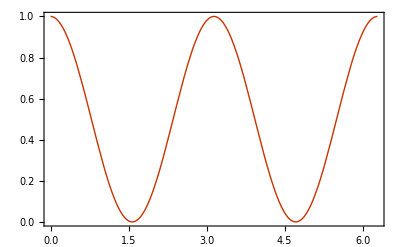

```mathematica
Plot[Cos[x]^2,{x,0,2π}]
```

```mathematica
Remove[t,c]
```

```mathematica
DSolve[{D[c[t,x,y],t]+0.5*Cos[x]*Sin[y]*D[c[t,x,y],x]+0.5*Sin[x]*Cos[y]*D[c[t,x,y],y]==D[c[t,x,y],x]+D[c[t,x,y],y],c[0,x,y]==Cos[x]^2},c[t,x,y],{t}]
```

{{c[t,x,y]→Cos[x]^2+(1.+0. ⅈ) ((0.+0. ⅈ)+(1.+0. ⅈ) c^(0,0,1)[K[1],x,y]-(0.25+0. ⅈ) Sin[x-1. y] c^(0,0,1)[K[1],x,y]-(0.25+0. ⅈ) Sin[x+y] c^(0,0,1)[K[1],x,y]+(1.+0. ⅈ) c^(0,1,0)[K[1],x,y]+(0.25+0. ⅈ) Sin[x-1. y] c^(0,1,0)[K[1],x,y]-(0.25+0. ⅈ) Sin[x+y] c^(0,1,0)[K[1],x,y])K[1]0t}}